```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large];
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;

Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
association=Append[association,rawFile[[k]][[1]]->StringJoin[ToString[DeleteCases[Take[rawFile[[k]],{2,-1}],Null]]]];
,
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];

StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 4 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 4 beta0]stokes[[1]]);
stokes];

StokesParametersFromRawFourierData[intensityArray_,rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
StokesParametersFromFourierCoefficients[fc,rev,alpha,beta0,delta]
];

StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_,rev_]:=
Module[{intensityArray,f},
intensityArray=Normal[polFile[[2]][All,"COUNT"]];
StokesParametersFromRawFourierData[intensityArray,rev,alpha,beta0,delta]
];

StokesParametersFromPolFileName[polFileName_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["#REV:"];
StokesParametersFromPolFile[f,alpha,beta0,delta,rev_]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];

AverageGetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetAverageCountRateFromFileNames[fileNames_]:=Module[{files},
files=ImportFile[fileNames];
GetAverageCountRateFromFiles[files]
];

(* See Nate Clayburn's explanation on Background Subtraction p. 129 eq. 93*)
(* Returns a list of two items.
	the first item is a list of the intensity reaching the PMT at each step of the polarimeter.
	the second item is the standard deviation of these counts
*)
GetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];


GetCurrentNormalizedAverageCountRateFromFiles[files_]:=Module[{t,scale,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,rev},
nDataPts=files[[1]][[1]]["#DATAPPR:"];
rev=files[[1]][[1]]["#REV:"];
(* This hasn't yet been implemented in the data collection files. As soon as it is, you can uncomment it.
scale=files[[1]][[1]]["#SCALE:"];*)
scale=6;
darkCountsRate=10;
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files]*rev;
t=dwell*nCycles;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/t/Abs[current[[j]]*10^(-scale)/(1*^-9)];
errorSum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/(t^2*(current[[j]]*10^(-scale)/(1*^-9))^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFileNames[fileNames_]:=Module[{filesPass,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
filesPass=ImportFile[fileNames];
GetCurrentNormalizedAverageCountRateFromFiles[filesPass]
];

AverageBackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
Print[darkCountsRate];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
rev=files[[i]][[1]]["#REV:"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageGetAverageCountRateFromFiles[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];
SignalRateCurrentNormFromRates::usage ="SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background."
SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["#DWELL(s):"];
nCycles=file[[1]]["#REV:"];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]/(nCycles*dwell)-(darkCountsRate[[1]][[j]])/nCycles)/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-(darkCountsRate[[2]][[j]])^2/(nCycles^2*current[[j]]^2)-(molyCountsRate[[2]][[j]])^2/(nCycles^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["#REV:"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

AverageStokes[stokesVectors_]:=Module[{i,transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes;
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=Mean[transposedValues[[i]]];
stokesStdDev[[i]]=StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
{stokes,stokesStdDev}
];

CalculateAverageStokesFromFilesAndCountRates[polFileNames_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes={0,0,0,0,0,0};
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];
Export["stokesValues.tsv",{polFileNames,stokesValues}];
AverageStokes[stokesValues]
]

NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];


GetIntensityArrayFromFileName[fileName_]:=Module[{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,{"ANGLE","COUNT"}]]
];

PlotRawPolFromFileName[fileName_]:=Module[
{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
ListPlot[intensityArray]
];
SetAttributes[PlotRawPolFromFileName,Listable];

PlotListOfPolFileNames[fileNames_,plotRange_:{Automatic,Automatic}]:=Module[{intensityArrays,i},
intensityArrays={};
For[i=1,i≤Length[fileNames],i++,
AppendTo[intensityArrays,Legended[GetIntensityArrayFromFileName[fileNames[[i]]],fileNames[[i]]]];
];
ListPlot[intensityArrays,PlotRange->plotRange]
];

GetStokesFromFileNames[fileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{i,stokes,signal,stokesData},
stokesData={};
signal=ImportFile[fileNames];
For[i=1,i≤Length[fileNames],i++,
stokes=StokesParametersFromPolFile[signal[[i]],alpha,beta,delta,signal[[i]][[1]]["#REV:"]];
AppendTo[stokesData,stokes];
];
stokesData
];
GetAverageFourierCoefficientsFromFileNames[fileNames]:=Module[{fc},
fc=GetFourierCoefficientsFromFileNames[fileNames]];

GetFourierCoefficientsFromFileNames[fileNames_]:=Module[{files,i,coefficientsList,intensityArray,revs},
files=ImportFile[fileNames];
coefficientsList={};
For[i=1,i≤Length[files],i++,
revs=files[[i]][[1]]["#REV:"];
intensityArray=Normal[files[[i]][[2]][All,"COUNT"]];
AppendTo[coefficientsList,DFT[intensityArray,revs]];
];
coefficientsList
];

GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames_,timeStamp_]:=Module[{exFileIndex,exFile,x},
exFileIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,timeStamp];
exFile=ImportFile[excitationFileNames[[exFileIndex]]];
aoutToElectronEnergyData=Normal[exFile[[2]][All,{"Aout","SecondaryElectronEnergy"}][[All,Values]]];
LinearModelFit[aoutToElectronEnergyData,x,x]
];
```

SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background.

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dropBoxfolderLaptop=FileNameJoin[{"/","home","karl","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,dataDump,pumpQWP,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-02-13","data"}]];
polFileNames=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]]
excitationFileNames=FileNames[StringExpression["EX",__,"_",__,DigitCharacter,".dat"]]
```

{POL2018-02-13_015129.dat,POL2018-02-13_015452.dat,POL2018-02-13_015814.dat,POL2018-02-13_020136.dat,POL2018-02-13_051034.dat,POL2018-02-13_051357.dat,POL2018-02-13_051719.dat,POL2018-02-13_052041.dat,POL2018-02-13_052402.dat,POL2018-02-13_052725.dat,POL2018-02-13_053047.dat,POL2018-02-13_053409.dat,POL2018-02-13_053731.dat,POL2018-02-13_054053.dat,POL2018-02-13_054415.dat,POL2018-02-13_054737.dat,POL2018-02-13_055101.dat,POL2018-02-13_055424.dat,POL2018-02-13_055746.dat,POL2018-02-13_060108.dat,POL2018-02-13_060429.dat,POL2018-02-13_060753.dat,POL2018-02-13_061115.dat,POL2018-02-13_061438.dat,POL2018-02-13_061759.dat,POL2018-02-13_062122.dat,POL2018-02-13_062444.dat,POL2018-02-13_062806.dat,POL2018-02-13_063127.dat,POL2018-02-13_063450.dat,POL2018-02-13_063812.dat,POL2018-02-13_064134.dat,POL2018-02-13_064456.dat,POL2018-02-13_064819.dat,POL2018-02-13_065142.dat,POL2018-02-13_065504.dat,POL2018-02-13_065825.dat,POL2018-02-13_070148.dat,POL2018-02-13_070512.dat,POL2018-02-13_070834.dat,POL2018-02-13_071156.dat,POL2018-02-13_071519.dat,POL2018-02-13_071840.dat,POL2018-02-13_072203.dat,POL2018-02-13_072524.dat,POL2018-02-13_072847.dat,POL2018-02-13_073209.dat,POL2018-02-13_073531.dat,POL2018-02-13_073852.dat,POL2018-02-13_074215.dat,POL2018-02-13_074537.dat,POL2018-02-13_074859.dat,POL2018-02-13_075221.dat,POL2018-02-13_075543.dat,POL2018-02-13_075905.dat,POL2018-02-13_080227.dat,POL2018-02-13_080549.dat,POL2018-02-13_080911.dat,POL2018-02-13_081233.dat,POL2018-02-13_081555.dat,POL2018-02-13_081917.dat,POL2018-02-13_082240.dat,POL2018-02-13_082601.dat,POL2018-02-13_082924.dat,POL2018-02-13_083245.dat,POL2018-02-13_083608.dat,POL2018-02-13_083930.dat,POL2018-02-13_084252.dat,POL2018-02-13_084613.dat,POL2018-02-13_084936.dat,POL2018-02-13_085258.dat,POL2018-02-13_085620.dat,POL2018-02-13_085942.dat,POL2018-02-13_090304.dat,POL2018-02-13_090626.dat,POL2018-02-13_090948.dat,POL2018-02-13_091310.dat,POL2018-02-13_091633.dat,POL2018-02-13_091954.dat,POL2018-02-13_092317.dat,POL2018-02-13_092638.dat,POL2018-02-13_093001.dat,POL2018-02-13_093323.dat,POL2018-02-13_093646.dat,POL2018-02-13_094008.dat,POL2018-02-13_094331.dat,POL2018-02-13_094654.dat,POL2018-02-13_095016.dat,POL2018-02-13_095337.dat,POL2018-02-13_095700.dat,POL2018-02-13_100022.dat,POL2018-02-13_100344.dat,POL2018-02-13_100706.dat,POL2018-02-13_101030.dat,POL2018-02-13_101352.dat,POL2018-02-13_101714.dat,POL2018-02-13_102036.dat,POL2018-02-13_102359.dat,POL2018-02-13_102721.dat,POL2018-02-13_103043.dat,POL2018-02-13_103404.dat,POL2018-02-13_103727.dat,POL2018-02-13_104049.dat,POL2018-02-13_104411.dat,POL2018-02-13_104733.dat,POL2018-02-13_105056.dat,POL2018-02-13_105418.dat,POL2018-02-13_105740.dat,POL2018-02-13_110102.dat,POL2018-02-13_110426.dat,POL2018-02-13_110749.dat,POL2018-02-13_111111.dat,POL2018-02-13_111433.dat,POL2018-02-13_111755.dat,POL2018-02-13_112117.dat,POL2018-02-13_112439.dat,POL2018-02-13_112801.dat,POL2018-02-13_113124.dat,POL2018-02-13_113445.dat,POL2018-02-13_113808.dat,POL2018-02-13_114129.dat,POL2018-02-13_114454.dat,POL2018-02-13_114816.dat,POL2018-02-13_115138.dat,POL2018-02-13_115500.dat,POL2018-02-13_115822.dat,POL2018-02-13_120144.dat,POL2018-02-13_120506.dat,POL2018-02-13_120828.dat,POL2018-02-13_121151.dat,POL2018-02-13_121512.dat,POL2018-02-13_121835.dat,POL2018-02-13_122156.dat,POL2018-02-13_122519.dat,POL2018-02-13_122841.dat,POL2018-02-13_123203.dat,POL2018-02-13_123525.dat,POL2018-02-13_123847.dat,POL2018-02-13_124209.dat,POL2018-02-13_124531.dat,POL2018-02-13_124853.dat,POL2018-02-13_125216.dat,POL2018-02-13_125538.dat,POL2018-02-13_125900.dat,POL2018-02-13_130221.dat,POL2018-02-13_130544.dat,POL2018-02-13_130906.dat,POL2018-02-13_131228.dat,POL2018-02-13_131550.dat,POL2018-02-13_131912.dat,POL2018-02-13_132234.dat,POL2018-02-13_132556.dat,POL2018-02-13_132918.dat,POL2018-02-13_133241.dat,POL2018-02-13_133603.dat,POL2018-02-13_133925.dat,POL2018-02-13_134246.dat,POL2018-02-13_134609.dat,POL2018-02-13_134931.dat,POL2018-02-13_135253.dat,POL2018-02-13_135615.dat,POL2018-02-13_135937.dat,POL2018-02-13_140259.dat,POL2018-02-13_140622.dat,POL2018-02-13_140943.dat,POL2018-02-13_141306.dat,POL2018-02-13_141628.dat,POL2018-02-13_141950.dat,POL2018-02-13_142311.dat,POL2018-02-13_142634.dat,POL2018-02-13_142956.dat,POL2018-02-13_143318.dat,POL2018-02-13_143640.dat,POL2018-02-13_144003.dat,POL2018-02-13_144324.dat,POL2018-02-13_144647.dat,POL2018-02-13_145008.dat,POL2018-02-13_145331.dat,POL2018-02-13_145653.dat,POL2018-02-13_150016.dat,POL2018-02-13_150339.dat,POL2018-02-13_150701.dat,POL2018-02-13_151023.dat,POL2018-02-13_151345.dat,POL2018-02-13_151707.dat,POL2018-02-13_152030.dat,POL2018-02-13_152351.dat,POL2018-02-13_152714.dat,POL2018-02-13_153035.dat,POL2018-02-13_153358.dat,POL2018-02-13_153720.dat,POL2018-02-13_154042.dat,POL2018-02-13_154404.dat,POL2018-02-13_154727.dat,POL2018-02-13_155049.dat,POL2018-02-13_155411.dat,POL2018-02-13_155732.dat,POL2018-02-13_160057.dat,POL2018-02-13_160419.dat,POL2018-02-13_160741.dat,POL2018-02-13_161103.dat,POL2018-02-13_161426.dat,POL2018-02-13_161747.dat,POL2018-02-13_162111.dat,POL2018-02-13_162433.dat,POL2018-02-13_162756.dat,POL2018-02-13_163118.dat,POL2018-02-13_163440.dat,POL2018-02-13_163802.dat,POL2018-02-13_164124.dat,POL2018-02-13_164125.dat,POL2018-02-13_164126.dat,POL2018-02-13_164127.dat,POL2018-02-13_164128.dat,POL2018-02-13_164129.dat,POL2018-02-13_164130.dat,POL2018-02-13_164131.dat,POL2018-02-13_164132.dat,POL2018-02-13_164133.dat,POL2018-02-13_164134.dat,POL2018-02-13_182500.dat,POL2018-02-13_182823.dat,POL2018-02-13_183145.dat,POL2018-02-13_183507.dat,POL2018-02-13_183829.dat,POL2018-02-13_184501.dat,POL2018-02-13_185133.dat,POL2018-02-13_185806.dat,POL2018-02-13_190437.dat,POL2018-02-13_190800.dat,POL2018-02-13_191122.dat,POL2018-02-13_191444.dat,POL2018-02-13_191806.dat,POL2018-02-13_192129.dat,POL2018-02-13_192452.dat,POL2018-02-13_192814.dat,POL2018-02-13_193136.dat,POL2018-02-13_193809.dat,POL2018-02-13_194441.dat,POL2018-02-13_195113.dat,POL2018-02-13_195745.dat,POL2018-02-13_200107.dat,POL2018-02-13_200429.dat,POL2018-02-13_200751.dat,POL2018-02-13_201113.dat,POL2018-02-13_201436.dat,POL2018-02-13_201757.dat,POL2018-02-13_202120.dat,POL2018-02-13_202441.dat,POL2018-02-13_203114.dat,POL2018-02-13_203746.dat,POL2018-02-13_204418.dat,POL2018-02-13_205050.dat,POL2018-02-13_205413.dat,POL2018-02-13_205735.dat,POL2018-02-13_210057.dat,POL2018-02-13_210419.dat,POL2018-02-13_210742.dat,POL2018-02-13_211106.dat,POL2018-02-13_211428.dat,POL2018-02-13_211750.dat,POL2018-02-13_212422.dat,POL2018-02-13_213054.dat,POL2018-02-13_213727.dat,POL2018-02-13_214358.dat,POL2018-02-13_214721.dat,POL2018-02-13_215043.dat,POL2018-02-13_215405.dat,POL2018-02-13_215726.dat,POL2018-02-13_220049.dat,POL2018-02-13_220412.dat,POL2018-02-13_220736.dat,POL2018-02-13_221058.dat,POL2018-02-13_221730.dat,POL2018-02-13_222402.dat,POL2018-02-13_223035.dat,POL2018-02-13_223706.dat,POL2018-02-13_224029.dat,POL2018-02-13_224351.dat,POL2018-02-13_224713.dat,POL2018-02-13_233536.dat,POL2018-02-13_233859.dat,POL2018-02-13_234221.dat,POL2018-02-13_234543.dat,POL2018-02-13_234905.dat,POL2018-02-13_235538.dat,POL2018-02-14_000211.dat,POL2018-02-14_000843.dat,POL2018-02-14_001515.dat,POL2018-02-14_001837.dat,POL2018-02-14_002159.dat,POL2018-02-14_002521.dat,POL2018-02-14_002843.dat,POL2018-02-14_003205.dat,POL2018-02-14_003527.dat,POL2018-02-14_003849.dat,POL2018-02-14_004211.dat,POL2018-02-14_004845.dat,POL2018-02-14_005517.dat,POL2018-02-14_010150.dat,POL2018-02-14_010821.dat,POL2018-02-14_011144.dat,POL2018-02-14_011506.dat,POL2018-02-14_011828.dat,POL2018-02-14_012150.dat,POL2018-02-14_012512.dat,POL2018-02-14_012834.dat,POL2018-02-14_013156.dat,POL2018-02-14_013518.dat,POL2018-02-14_014151.dat,POL2018-02-14_014823.dat,POL2018-02-14_015455.dat,POL2018-02-14_020126.dat,POL2018-02-14_020449.dat,POL2018-02-14_020811.dat,POL2018-02-14_021133.dat,POL2018-02-14_021455.dat,POL2018-02-14_021817.dat,POL2018-02-14_022139.dat,POL2018-02-14_022501.dat,POL2018-02-14_022823.dat,POL2018-02-14_023456.dat,POL2018-02-14_024128.dat,POL2018-02-14_024800.dat,POL2018-02-14_025432.dat,POL2018-02-14_025754.dat,POL2018-02-14_030116.dat,POL2018-02-14_030438.dat,POL2018-02-14_030800.dat,POL2018-02-14_031123.dat,POL2018-02-14_031444.dat,POL2018-02-14_031807.dat,POL2018-02-14_032130.dat,POL2018-02-14_032803.dat,POL2018-02-14_033435.dat,POL2018-02-14_034109.dat,POL2018-02-14_034741.dat,POL2018-02-14_035104.dat,POL2018-02-14_035425.dat,POL2018-02-14_035747.dat,POL2018-02-14_044618.dat,POL2018-02-14_044941.dat,POL2018-02-14_045303.dat,POL2018-02-14_045625.dat,POL2018-02-14_045947.dat,POL2018-02-14_050620.dat,POL2018-02-14_051251.dat,POL2018-02-14_051926.dat,POL2018-02-14_052557.dat,POL2018-02-14_052920.dat,POL2018-02-14_053242.dat,POL2018-02-14_053604.dat,POL2018-02-14_053926.dat,POL2018-02-14_054248.dat,POL2018-02-14_054610.dat,POL2018-02-14_054932.dat,POL2018-02-14_055254.dat,POL2018-02-14_055927.dat,POL2018-02-14_060559.dat,POL2018-02-14_061231.dat,POL2018-02-14_061903.dat,POL2018-02-14_062225.dat,POL2018-02-14_062547.dat,POL2018-02-14_062909.dat,POL2018-02-14_063231.dat,POL2018-02-14_063553.dat,POL2018-02-14_063915.dat,POL2018-02-14_064237.dat,POL2018-02-14_064559.dat,POL2018-02-14_065233.dat,POL2018-02-14_065905.dat,POL2018-02-14_070538.dat,POL2018-02-14_071209.dat,POL2018-02-14_071532.dat,POL2018-02-14_071854.dat,POL2018-02-14_072216.dat,POL2018-02-14_072538.dat,POL2018-02-14_072900.dat,POL2018-02-14_073222.dat,POL2018-02-14_073544.dat,POL2018-02-14_073906.dat,POL2018-02-14_074539.dat,POL2018-02-14_075211.dat,POL2018-02-14_075843.dat,POL2018-02-14_080514.dat,POL2018-02-14_080837.dat,POL2018-02-14_081159.dat,POL2018-02-14_081521.dat,POL2018-02-14_081843.dat,POL2018-02-14_082206.dat,POL2018-02-14_082527.dat,POL2018-02-14_082852.dat,POL2018-02-14_083213.dat,POL2018-02-14_083846.dat,POL2018-02-14_084518.dat,POL2018-02-14_085150.dat,POL2018-02-14_085822.dat,POL2018-02-14_090145.dat,POL2018-02-14_090506.dat,POL2018-02-14_090830.dat,POL2018-02-14_093846.dat,POL2018-02-14_120341.dat,POL2018-02-14_120703.dat,POL2018-02-14_121025.dat,POL2018-02-14_121347.dat,POL2018-02-14_121709.dat,POL2018-02-14_122034.dat,POL2018-02-14_122355.dat,POL2018-02-14_122718.dat,POL2018-02-14_123039.dat,POL2018-02-14_123402.dat,POL2018-02-14_123724.dat,POL2018-02-14_124046.dat,POL2018-02-14_131847.dat,POL2018-02-14_132210.dat,POL2018-02-14_132531.dat,POL2018-02-14_132854.dat,POL2018-02-14_133215.dat,POL2018-02-14_133538.dat,POL2018-02-14_133901.dat,POL2018-02-14_134223.dat,POL2018-02-14_134545.dat,POL2018-02-14_134907.dat,POL2018-02-14_135229.dat,POL2018-02-14_135551.dat,POL2018-02-14_142130.dat,POL2018-02-14_142453.dat,POL2018-02-14_142815.dat,POL2018-02-14_143137.dat,POL2018-02-14_143458.dat,POL2018-02-14_143821.dat,POL2018-02-14_144143.dat,POL2018-02-14_144505.dat,POL2018-02-14_144827.dat,POL2018-02-14_145149.dat,POL2018-02-14_145511.dat,POL2018-02-14_145834.dat,POL2018-02-14_162440.dat,POL2018-02-14_162803.dat,POL2018-02-14_163125.dat,POL2018-02-14_163447.dat,POL2018-02-14_163808.dat,POL2018-02-14_164442.dat,POL2018-02-14_165116.dat,POL2018-02-14_165748.dat,POL2018-02-14_170420.dat,POL2018-02-14_170743.dat,POL2018-02-14_171105.dat,POL2018-02-14_171427.dat,POL2018-02-14_171753.dat,POL2018-02-14_172116.dat,POL2018-02-14_172438.dat,POL2018-02-14_172800.dat,POL2018-02-14_173121.dat,POL2018-02-14_173754.dat,POL2018-02-14_174426.dat,POL2018-02-14_175059.dat,POL2018-02-14_175730.dat,POL2018-02-14_180053.dat,POL2018-02-14_180415.dat,POL2018-02-14_180738.dat,POL2018-02-14_181106.dat,POL2018-02-14_181428.dat,POL2018-02-14_181750.dat,POL2018-02-14_182112.dat,POL2018-02-14_182433.dat,POL2018-02-14_183106.dat,POL2018-02-14_183738.dat,POL2018-02-14_184410.dat,POL2018-02-14_185042.dat,POL2018-02-14_185405.dat,POL2018-02-14_185727.dat,POL2018-02-14_190049.dat,POL2018-02-14_203704.dat,POL2018-02-14_204027.dat,POL2018-02-14_204348.dat,POL2018-02-14_204711.dat,POL2018-02-14_205032.dat,POL2018-02-14_205706.dat,POL2018-02-14_210339.dat,POL2018-02-14_211011.dat,POL2018-02-14_211642.dat,POL2018-02-14_212005.dat,POL2018-02-14_212327.dat,POL2018-02-14_212649.dat,POL2018-02-14_213016.dat,POL2018-02-14_213338.dat,POL2018-02-14_213702.dat,POL2018-02-14_214026.dat,POL2018-02-14_214348.dat,POL2018-02-14_215021.dat,POL2018-02-14_215653.dat,POL2018-02-14_220325.dat,POL2018-02-14_220956.dat,POL2018-02-14_221319.dat,POL2018-02-14_221641.dat,POL2018-02-14_222003.dat,POL2018-02-14_222330.dat,POL2018-02-14_222652.dat,POL2018-02-14_223014.dat,POL2018-02-14_223336.dat,POL2018-02-14_223657.dat,POL2018-02-14_224330.dat,POL2018-02-14_225002.dat,POL2018-02-14_225634.dat,POL2018-02-14_230306.dat,POL2018-02-14_230629.dat,POL2018-02-14_230951.dat,POL2018-02-14_231313.dat,POL2018-02-15_021557.dat,POL2018-02-15_021920.dat,POL2018-02-15_022241.dat,POL2018-02-15_022604.dat,POL2018-02-15_022930.dat,POL2018-02-15_023603.dat,POL2018-02-15_024234.dat,POL2018-02-15_024907.dat,POL2018-02-15_025543.dat,POL2018-02-15_025908.dat,POL2018-02-15_030230.dat,POL2018-02-15_030552.dat,POL2018-02-15_030918.dat,POL2018-02-15_031241.dat,POL2018-02-15_031602.dat,POL2018-02-15_031925.dat,POL2018-02-15_032251.dat,POL2018-02-15_032924.dat,POL2018-02-15_033555.dat,POL2018-02-15_034228.dat,POL2018-02-15_034904.dat,POL2018-02-15_035227.dat,POL2018-02-15_035548.dat,POL2018-02-15_035911.dat,POL2018-02-15_040237.dat,POL2018-02-15_040600.dat,POL2018-02-15_040921.dat,POL2018-02-15_041244.dat,POL2018-02-15_041610.dat,POL2018-02-15_042243.dat,POL2018-02-15_042915.dat,POL2018-02-15_043548.dat,POL2018-02-15_044224.dat,POL2018-02-15_044547.dat,POL2018-02-15_044908.dat,POL2018-02-15_045230.dat,POL2018-02-15_045557.dat,POL2018-02-15_045919.dat,POL2018-02-15_050241.dat,POL2018-02-15_050603.dat,POL2018-02-15_050930.dat,POL2018-02-15_051602.dat,POL2018-02-15_052234.dat,POL2018-02-15_052906.dat,POL2018-02-15_053543.dat,POL2018-02-15_053905.dat,POL2018-02-15_054227.dat,POL2018-02-15_054549.dat,POL2018-02-15_054916.dat,POL2018-02-15_055238.dat,POL2018-02-15_055600.dat,POL2018-02-15_055922.dat,POL2018-02-15_060249.dat,POL2018-02-15_060921.dat,POL2018-02-15_061553.dat,POL2018-02-15_062225.dat,POL2018-02-15_062902.dat,POL2018-02-15_063224.dat,POL2018-02-15_063546.dat,POL2018-02-15_063908.dat,POL2018-02-15_100545.dat,POL2018-02-15_100804.dat,POL2018-02-15_101022.dat,POL2018-02-15_101241.dat,POL2018-02-15_101504.dat,POL2018-02-15_101723.dat,POL2018-02-15_101943.dat,POL2018-02-15_102202.dat,POL2018-02-15_102425.dat,POL2018-02-15_102644.dat,POL2018-02-15_102902.dat,POL2018-02-15_103121.dat,POL2018-02-15_103845.dat,POL2018-02-15_104104.dat,POL2018-02-15_104323.dat,POL2018-02-15_104541.dat,POL2018-02-15_104805.dat,POL2018-02-15_105023.dat,POL2018-02-15_105242.dat,POL2018-02-15_105501.dat,POL2018-02-15_112826.dat,POL2018-02-15_113045.dat,POL2018-02-15_113303.dat,POL2018-02-15_113522.dat,POL2018-02-15_113745.dat,POL2018-02-15_114004.dat,POL2018-02-15_114223.dat,POL2018-02-15_114441.dat,POL2018-02-15_114705.dat,POL2018-02-15_114924.dat,POL2018-02-15_115142.dat,POL2018-02-15_115401.dat,POL2018-02-15_115624.dat,POL2018-02-15_115843.dat,POL2018-02-15_120101.dat,POL2018-02-15_120320.dat,POL2018-02-15_140631.dat,POL2018-02-15_140850.dat,POL2018-02-15_141110.dat,POL2018-02-15_141328.dat,POL2018-02-15_141552.dat,POL2018-02-15_141811.dat,POL2018-02-15_142029.dat,POL2018-02-15_142248.dat,POL2018-02-15_142511.dat,POL2018-02-15_142730.dat,POL2018-02-15_142949.dat,POL2018-02-15_143207.dat,POL2018-02-15_143832.dat,POL2018-02-15_144051.dat,POL2018-02-15_144310.dat,POL2018-02-15_144529.dat,POL2018-02-15_144752.dat,POL2018-02-15_145011.dat,POL2018-02-15_145229.dat,POL2018-02-15_145448.dat,POL2018-02-15_145711.dat,POL2018-02-15_145930.dat,POL2018-02-15_150149.dat,POL2018-02-15_150409.dat,POL2018-02-15_152155.dat,POL2018-02-15_152414.dat,POL2018-02-15_152633.dat,POL2018-02-15_152853.dat,POL2018-02-15_153117.dat,POL2018-02-15_153336.dat,POL2018-02-15_153554.dat,POL2018-02-15_153813.dat,POL2018-02-15_154036.dat,POL2018-02-15_154255.dat,POL2018-02-15_154514.dat,POL2018-02-15_154732.dat,POL2018-02-15_163357.dat,POL2018-02-15_163616.dat,POL2018-02-15_163835.dat,POL2018-02-15_164053.dat,POL2018-02-15_164312.dat,POL2018-02-15_164634.dat,POL2018-02-15_164956.dat,POL2018-02-15_165319.dat,POL2018-02-15_165642.dat,POL2018-02-15_165901.dat,POL2018-02-15_170120.dat,POL2018-02-15_170339.dat,POL2018-02-15_171024.dat,POL2018-02-15_171243.dat,POL2018-02-15_171501.dat,POL2018-02-15_171720.dat,POL2018-02-15_171938.dat,POL2018-02-15_172301.dat,POL2018-02-15_172623.dat,POL2018-02-15_172946.dat,POL2018-02-15_173308.dat,POL2018-02-15_173528.dat,POL2018-02-15_173746.dat,POL2018-02-15_174005.dat,POL2018-02-15_174650.dat,POL2018-02-15_174909.dat,POL2018-02-15_175127.dat,POL2018-02-15_175346.dat,POL2018-02-15_175604.dat,POL2018-02-15_175927.dat,POL2018-02-15_180249.dat,POL2018-02-15_180611.dat,POL2018-02-15_180932.dat,POL2018-02-15_181152.dat,POL2018-02-15_181410.dat,POL2018-02-15_181629.dat,POL2018-02-15_200025.dat,POL2018-02-15_200244.dat,POL2018-02-15_200502.dat,POL2018-02-15_200721.dat,POL2018-02-15_200939.dat,POL2018-02-15_201302.dat,POL2018-02-15_201624.dat,POL2018-02-15_201946.dat,POL2018-02-15_202307.dat,POL2018-02-15_202527.dat,POL2018-02-15_202746.dat,POL2018-02-15_203005.dat,POL2018-02-15_203650.dat,POL2018-02-15_203909.dat,POL2018-02-15_204127.dat,POL2018-02-15_204346.dat,POL2018-02-15_204604.dat,POL2018-02-15_204927.dat,POL2018-02-15_205248.dat,POL2018-02-15_205612.dat,POL2018-02-15_205934.dat,POL2018-02-15_210153.dat,POL2018-02-15_210412.dat,POL2018-02-15_210631.dat,POL2018-02-15_211316.dat,POL2018-02-15_211535.dat,POL2018-02-15_211753.dat,POL2018-02-15_212012.dat,POL2018-02-15_212230.dat,POL2018-02-15_212553.dat,POL2018-02-15_212915.dat,POL2018-02-15_213237.dat,POL2018-02-15_213559.dat,POL2018-02-15_213818.dat,POL2018-02-15_214036.dat,POL2018-02-15_214255.dat,POL2018-02-15_232701.dat,POL2018-02-15_232920.dat,POL2018-02-15_233140.dat,POL2018-02-15_233358.dat,POL2018-02-15_233617.dat,POL2018-02-15_233939.dat,POL2018-02-15_234301.dat,POL2018-02-15_234623.dat,POL2018-02-15_234945.dat,POL2018-02-15_235204.dat,POL2018-02-15_235425.dat,POL2018-02-15_235644.dat,POL2018-02-16_000330.dat,POL2018-02-16_000550.dat,POL2018-02-16_000809.dat,POL2018-02-16_001028.dat,POL2018-02-16_001246.dat,POL2018-02-16_001609.dat,POL2018-02-16_001930.dat,POL2018-02-16_002253.dat,POL2018-02-16_002614.dat,POL2018-02-16_002834.dat,POL2018-02-16_003052.dat,POL2018-02-16_003311.dat,POL2018-02-16_003956.dat,POL2018-02-16_004215.dat,POL2018-02-16_004433.dat,POL2018-02-16_004652.dat,POL2018-02-16_004910.dat,POL2018-02-16_005233.dat,POL2018-02-16_005555.dat,POL2018-02-16_005917.dat,POL2018-02-16_010239.dat,POL2018-02-16_010458.dat,POL2018-02-16_010717.dat,POL2018-02-16_010935.dat}

{EX2018-02-13_013554.dat,EX2018-02-13_014854.dat,EX2018-02-13_023109.dat,EX2018-02-13_023357.dat,EX2018-02-13_050758.dat,EX2018-02-13_170321.dat,EX2018-02-13_173556.dat,EX2018-02-13_174047.dat,EX2018-02-13_182224.dat,EX2018-02-13_230939.dat,EX2018-02-13_233300.dat,EX2018-02-14_042016.dat,EX2018-02-14_044342.dat,EX2018-02-14_093056.dat,EX2018-02-14_113518.dat,EX2018-02-14_120100.dat,EX2018-02-14_131606.dat,EX2018-02-14_141849.dat,EX2018-02-14_162159.dat,EX2018-02-14_192323.dat,EX2018-02-14_203423.dat,EX2018-02-14_233539.dat,EX2018-02-15_002525.dat,EX2018-02-15_003357.dat,EX2018-02-15_003745.dat,EX2018-02-15_004024.dat,EX2018-02-15_021316.dat,EX2018-02-15_070136.dat,EX2018-02-15_100305.dat,EX2018-02-15_103605.dat,EX2018-02-15_133955.dat,EX2018-02-15_134120.dat,EX2018-02-15_135231.dat,EX2018-02-15_135300.dat,EX2018-02-15_140351.dat,EX2018-02-15_143552.dat,EX2018-02-15_151349.dat,EX2018-02-15_151914.dat,EX2018-02-15_163116.dat,EX2018-02-15_170742.dat,EX2018-02-15_174409.dat,EX2018-02-15_182033.dat,EX2018-02-15_184246.dat,EX2018-02-15_195744.dat,EX2018-02-15_203408.dat,EX2018-02-15_211035.dat,EX2018-02-15_214659.dat,EX2018-02-15_220910.dat,EX2018-02-15_232420.dat,EX2018-02-16_000049.dat,EX2018-02-16_003715.dat,EX2018-02-16_011339.dat,EX2018-02-16_013558.dat}

```mathematica
fit=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,"183912"];
```

Part::pkspec1: The expression index$408933 cannot be used as a part specification.

Import::chtype: First argument {EX2018-02-13_013554.dat,EX2018-02-13_014854.dat,EX2018-02-13_023109.dat,EX2018-02-13_023357.dat,EX2018-02-13_050758.dat,EX2018-02-13_170321.dat,EX2018-02-13_173556.dat,EX2018-02-13_174047.dat,EX2018-02-13_182224.dat,EX2018-02-13_230939.dat,EX2018-02-13_233300.dat,EX2018-02-14_042016.dat,EX2018-02-14_044342.dat,EX2018-02-14_093056.dat,EX2018-02-14_113518.dat,«21»,EX2018-02-15_151349.dat,EX2018-02-15_151914.dat,EX2018-02-15_163116.dat,EX2018-02-15_170742.dat,EX2018-02-15_174409.dat,EX2018-02-15_182033.dat,EX2018-02-15_184246.dat,EX2018-02-15_195744.dat,EX2018-02-15_203408.dat,EX2018-02-15_211035.dat,EX2018-02-15_214659.dat,EX2018-02-15_220910.dat,EX2018-02-15_232420.dat,EX2018-02-16_000049.dat,«3»}⟦index$408933⟧ is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Import::chtype: First argument {EX2018-02-13_013554.dat,EX2018-02-13_014854.dat,EX2018-02-13_023109.dat,EX2018-02-13_023357.dat,EX2018-02-13_050758.dat,EX2018-02-13_170321.dat,EX2018-02-13_173556.dat,EX2018-02-13_174047.dat,EX2018-02-13_182224.dat,EX2018-02-13_230939.dat,EX2018-02-13_233300.dat,EX2018-02-14_042016.dat,EX2018-02-14_044342.dat,EX2018-02-14_093056.dat,EX2018-02-14_113518.dat,«21»,EX2018-02-15_151349.dat,EX2018-02-15_151914.dat,EX2018-02-15_163116.dat,EX2018-02-15_170742.dat,EX2018-02-15_174409.dat,EX2018-02-15_182033.dat,EX2018-02-15_184246.dat,EX2018-02-15_195744.dat,EX2018-02-15_203408.dat,EX2018-02-15_211035.dat,EX2018-02-15_214659.dat,EX2018-02-15_220910.dat,EX2018-02-15_232420.dat,EX2018-02-16_000049.dat,«3»}⟦index$408933⟧ is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,-1},All].

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

```mathematica
runs=3; (*The number of Electron Polarization Runs*)
aouts={240,480,792};  (* A list of the AOUTs or energies at which we collected data*)
energies=aouts;
aoutToEnergy=GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames,"232420"];
For[i=1,i≤Length[aouts],i++,energies[[i]]=aoutToEnergy[aouts[[i]]]];
startFile=GetIndexOfFilenameFromTimestamp[polFileNames,"232701"];
pumpLights={"noPump","piPump","s+pump","s-pump"};
fileNames=polFileNames;

category1=pumpLights;
category2=energies;
allFiles=<||>;
subsetFiles=<||>;
files={};
Length[polFileNames]
Length[category1]*Length[category2]*runs

For[j=1,j<=Length[category1],j++,
For[i=1,i<=Length[category2],i++,
firstFile=((startFile-1)+i)+(j-1)*Length[category2];
lastFile=((startFile-1)+i+(j-1)*Length[category2])+(Length[category2]*Length[category1]*(runs-1));
listOfNames=Take[fileNames,{firstFile,lastFile,Length[category1]*Length[category2]}];
AppendTo[subsetFiles,category2[[i]]->listOfNames];
AppendTo[files,<|"cat1"-> category1[[j]],"cat2"->category2[[i]],"fileNames"-> listOfNames|>];
];
AppendTo[allFiles,category1[[j]]->subsetFiles];
];
allFiles;
files
```

749

36

{<|cat1→noPump,cat2→32.4584,fileNames→{POL2018-02-15_232701.dat,POL2018-02-16_000330.dat,POL2018-02-16_003956.dat}|>,<|cat1→noPump,cat2→25.0167,fileNames→{POL2018-02-15_232920.dat,POL2018-02-16_000550.dat,POL2018-02-16_004215.dat}|>,<|cat1→noPump,cat2→15.3426,fileNames→{POL2018-02-15_233140.dat,POL2018-02-16_000809.dat,POL2018-02-16_004433.dat}|>,<|cat1→piPump,cat2→32.4584,fileNames→{POL2018-02-15_233358.dat,POL2018-02-16_001028.dat,POL2018-02-16_004652.dat}|>,<|cat1→piPump,cat2→25.0167,fileNames→{POL2018-02-15_233617.dat,POL2018-02-16_001246.dat,POL2018-02-16_004910.dat}|>,<|cat1→piPump,cat2→15.3426,fileNames→{POL2018-02-15_233939.dat,POL2018-02-16_001609.dat,POL2018-02-16_005233.dat}|>,<|cat1→s+pump,cat2→32.4584,fileNames→{POL2018-02-15_234301.dat,POL2018-02-16_001930.dat,POL2018-02-16_005555.dat}|>,<|cat1→s+pump,cat2→25.0167,fileNames→{POL2018-02-15_234623.dat,POL2018-02-16_002253.dat,POL2018-02-16_005917.dat}|>,<|cat1→s+pump,cat2→15.3426,fileNames→{POL2018-02-15_234945.dat,POL2018-02-16_002614.dat,POL2018-02-16_010239.dat}|>,<|cat1→s-pump,cat2→32.4584,fileNames→{POL2018-02-15_235204.dat,POL2018-02-16_002834.dat,POL2018-02-16_010458.dat}|>,<|cat1→s-pump,cat2→25.0167,fileNames→{POL2018-02-15_235425.dat,POL2018-02-16_003052.dat,POL2018-02-16_010717.dat}|>,<|cat1→s-pump,cat2→15.3426,fileNames→{POL2018-02-15_235644.dat,POL2018-02-16_003311.dat,POL2018-02-16_010935.dat}|>}

```mathematica
allFileNames=Flatten[Normal[Dataset[files][Select[#cat2>26&]][All,"fileNames"]]]
```

{POL2018-02-15_232701.dat,POL2018-02-16_000330.dat,POL2018-02-16_003956.dat,POL2018-02-15_233358.dat,POL2018-02-16_001028.dat,POL2018-02-16_004652.dat,POL2018-02-15_234301.dat,POL2018-02-16_001930.dat,POL2018-02-16_005555.dat,POL2018-02-15_235204.dat,POL2018-02-16_002834.dat,POL2018-02-16_010458.dat}

## Taking the average counts from all the runs and manipulating beta to minimize P_2

```mathematica
cr=DFT[GetAverageCountRateFromFileNames[allFileNames][[1]],1]
plotRange=.05
alpha=20.4;
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[cr,1,alpha*π/180,beta*π/180,delta],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-plotRange,plotRange}}],{beta,0.001,90,.1}]
```

{{{0.,15.4055,-15.9326,7.96453,-103.322,-3.29283,9.29524,3.54754,-1.46895,-4.36264,3.1205,-4.01309,-1.86252,-1.30371,-3.36033,-1.66111,-2.92013,-2.73343,2.45943,1.20871,-1.56727,0.0325035,-2.68411,1.38382,-4.82635,1.44144,3.02626,10.6651,3.64137,0.995982},{}},{{4998.08,-0.207953,-1.05239,-3.29378,77.6038,6.8681,4.38007,-1.9274,5.36337,2.27254,4.40347,-0.565397,0.822513,-1.76148,-0.807025,3.31481,0.788909,-2.23025,1.26044,-2.76475,-0.271991,7.5907,2.11251,2.66405,-3.57043,2.39764,1.27862,0.504612,5.68489,1.62135},{}}}

0.05

## This time, taking all of the no Pump runs and manipulating beta to minimize P3:C2 (5)

```mathematica
cr=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[1]][[2]],allFiles[[1]][[3]],allFiles[[2]][[2]],allFiles[[2]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[cr,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.001,180,.1},{beta,0.001,90,.1}]
```

{{{0.,1.1784,2.62001,0.284943,-17.5553,1.18104,0.503914,0.85219,1.04702,0.738895,0.256199,-0.892243,1.91462,-0.0190515,-1.84368,0.202778,-2.32686,0.192369,-1.19313,0.387646,-1.38444,-1.56172,-1.41061,0.157624,-2.42745,-1.8741,0.565086,-1.77583,0.185493,-0.736445},{}},{{799.559,-1.25906,1.61471,0.651857,18.0906,0.25205,-0.268724,0.605558,1.04297,-0.902889,0.332639,1.91982,0.724006,-1.01814,0.134614,2.09861,-0.330684,1.00172,0.881919,1.65872,-0.771528,-2.33619,0.559578,-1.18869,0.210021,-1.46316,0.250819,1.95389,2.11104,0.200457},{}}}

Part::partd: Part specification cr⟦2⟧ is longer than depth of object.

Part::partd: Part specification cr⟦1⟧ is longer than depth of object.

Part::partd: Part specification cr⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 5 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«10»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 5 of {{286.136,283.645,279.805,277.572,275.656,274.333,273.382,274.803,276.49,278.558,280.095,282.817,285.097,285.573,285.04,284.448,281.501,278.319,276.207,273.02,«11»,282.289,279.169,276.833,273.191,272.1,272.011,272.013,274.065,276.57,278.939,281.78,283.122,283.969,283.161,282.222,278.644,276.561,273.16,270.971,«10»}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«10»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

## Now all S+ runs, maximize P3:C2

```mathematica
crPlus=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[3]][[2]],allFiles[[3]][[3]]]][[1]],1]
alpha=20.4;
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[crPlus,1,alpha*π/180,beta*π/180,delta],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{beta,0.01,90,.5}]
```

{{{0.,15.9783,8.84073,8.76767,6.16469,3.84606,3.71576,3.57696,2.27337,3.67394,1.85313,2.68532,1.97738,1.50719,3.35176,1.60648,1.65544,1.75761,0.142342,0.612677,2.99019,-0.302287,-0.249697,-0.231348,-0.159175,-1.44792,0.741447,0.488242,0.161798,0.190999},{}},{{323.535,10.0434,4.56412,3.6275,2.08363,3.77722,2.56247,2.69799,2.07537,2.46184,3.78843,2.77436,3.53605,1.71267,2.05445,2.23241,1.03084,2.57497,2.49725,0.998018,1.38843,1.75051,2.03643,0.530013,1.45423,2.19592,2.99638,2.54348,0.944892,1.3107},{}}}

## Now all S- runs, maximize P3:C2

```mathematica
crMinus=DFT[GetAverageCountRateFromFileNames[Join[allFiles[[4]][[2]],allFiles[[4]][[3]]]][[1]],1]
Manipulate[ListPlot[StokesParametersFromFourierCoefficients[crMinus,1,alpha*π/180,beta*π/180,π/2],PlotLabel->"Beta ="<>ToString[beta]<>", alpha= "<>ToString[alpha],PlotRange->{Automatic,{-.1,.1}}],{alpha,0.01,180,.5},{beta,0.01,90,.5}]
```

{{{0.,1.78115,-0.303387,-1.83037,-17.3361,0.163115,1.52605,-0.171453,-0.368338,-1.02368,-1.23842,-0.846395,-3.96541,-2.08349,1.10373,2.17667,-0.707989,0.0903758,0.314222,-0.720683,1.93701,-2.06505,1.00703,1.5837,1.10669,-1.32645,2.50454,0.364977,-0.493443,0.510236},{}},{{794.387,-2.24751,-0.33663,3.08742,17.7552,-0.386699,-2.20388,-1.68475,-2.0385,0.377871,-0.488333,1.05104,3.92549,0.642063,1.66628,0.37,0.513277,1.20567,0.095545,-1.14813,1.38833,0.031484,-0.972415,-2.52234,-2.00382,-0.473301,0.00609991,-2.35011,2.02337,-1.57636},{}}}

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦1⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦1⟧ is longer than depth of object.

Part::partd: Part specification crMinus⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
colorBlindPallete
```

{RGBColor[Rational[46, 51], Rational[53, 85], 0],RGBColor[Rational[86, 255], Rational[12, 17], Rational[233, 255]],RGBColor[0, Rational[158, 255], Rational[23, 51]],RGBColor[Rational[16, 17], Rational[76, 85], Rational[22, 85]],RGBColor[0, Rational[38, 85], Rational[178, 255]],RGBColor[Rational[71, 85], Rational[94, 255], 0],RGBColor[Rational[4, 5], Rational[121, 255], Rational[167, 255]],RGBColor[0, 0, 0]}

```mathematica
Rasterize[energyPlots[[2]],ImageResolution->200]
```

-Graphics-

## Display all raw data and averages

Pump Light: noPump, Energy: 22.63

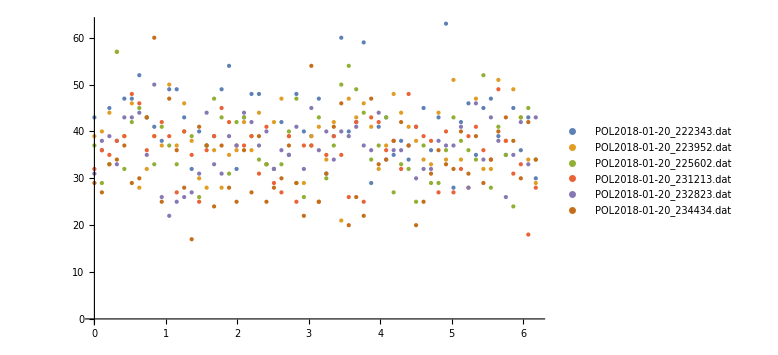

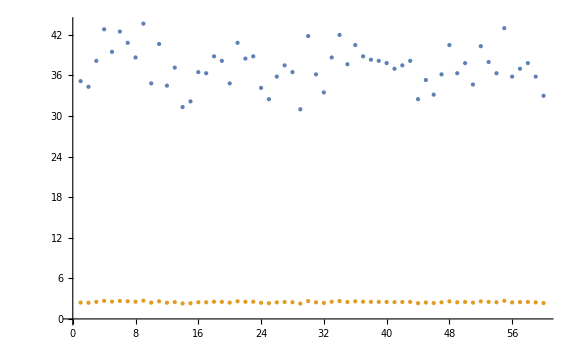

Pump Light: noPump, Energy: 27.49

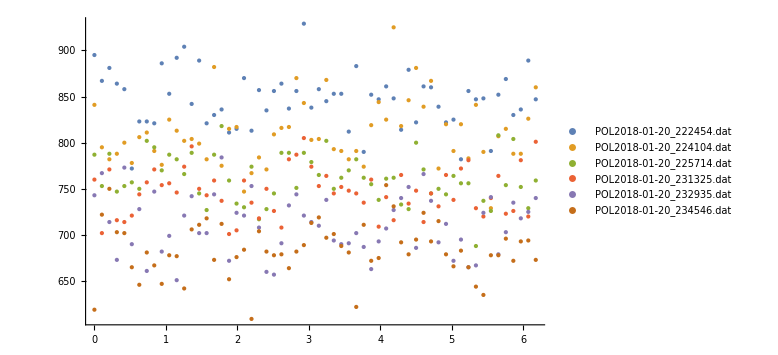

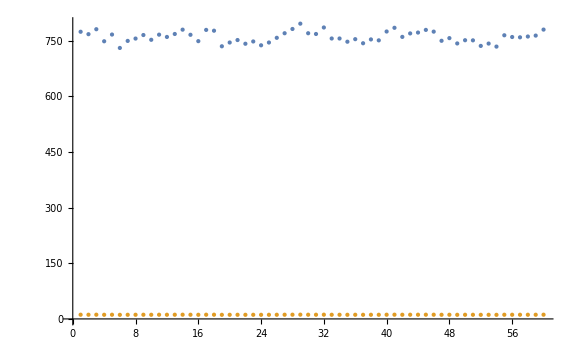

Pump Light: noPump, Energy: 36.55

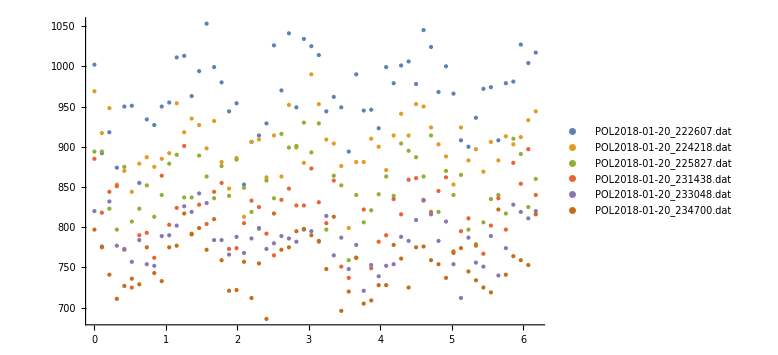

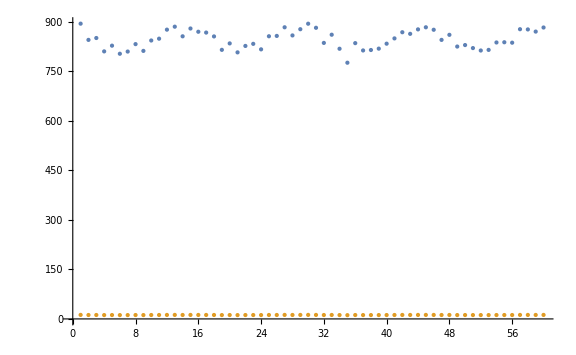

Pump Light: piPump, Energy: 22.63

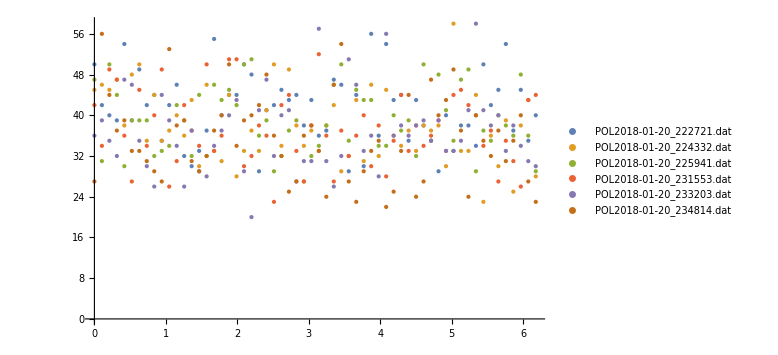

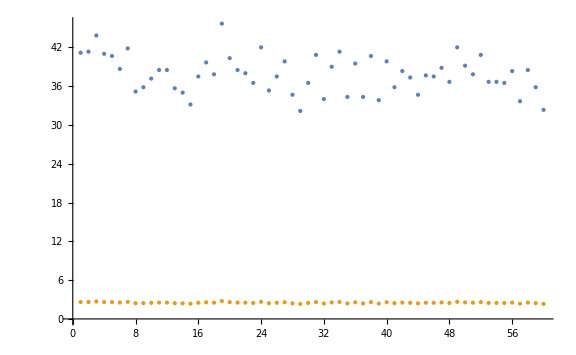

Pump Light: piPump, Energy: 27.49

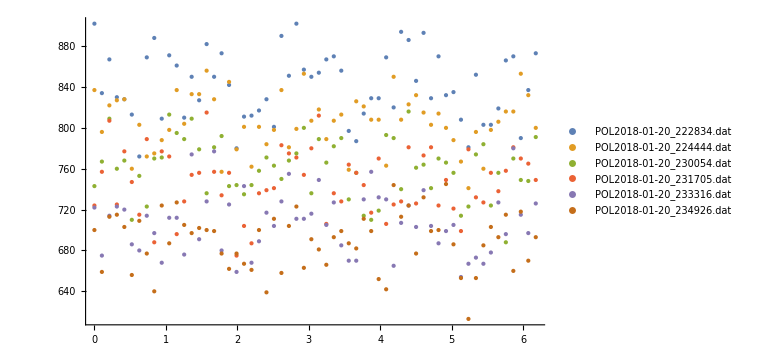

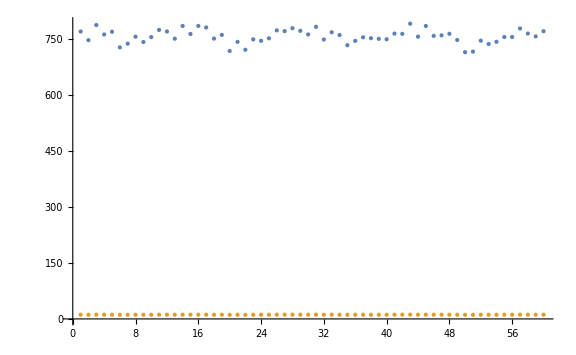

Pump Light: piPump, Energy: 36.55

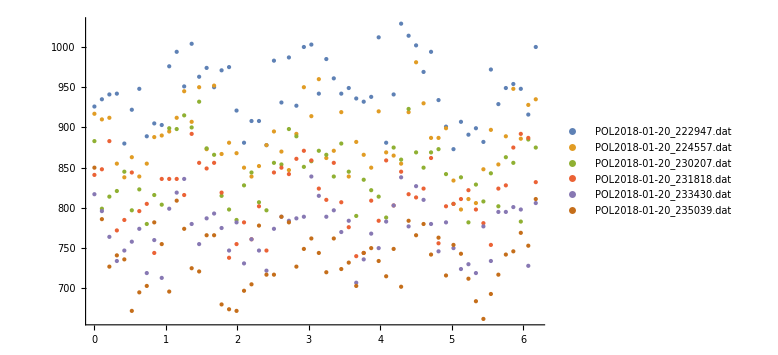

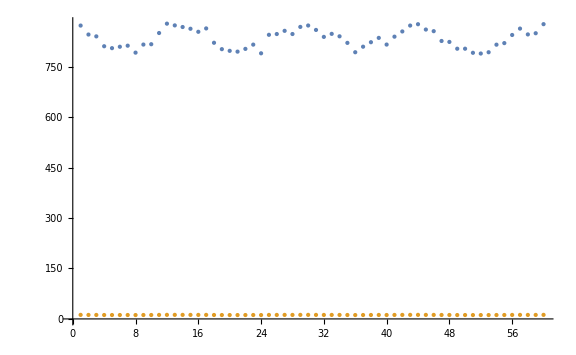

Pump Light: s+Pump, Energy: 22.63

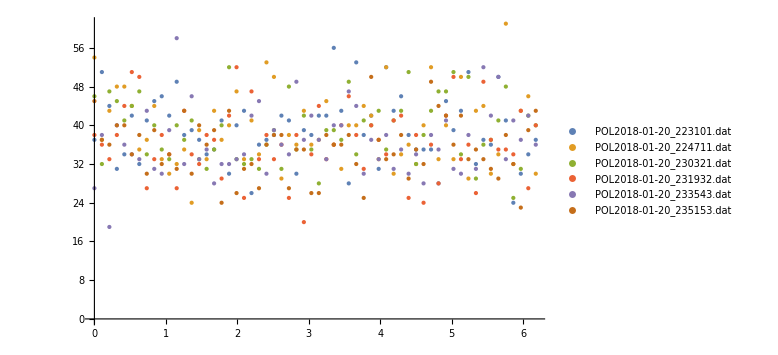

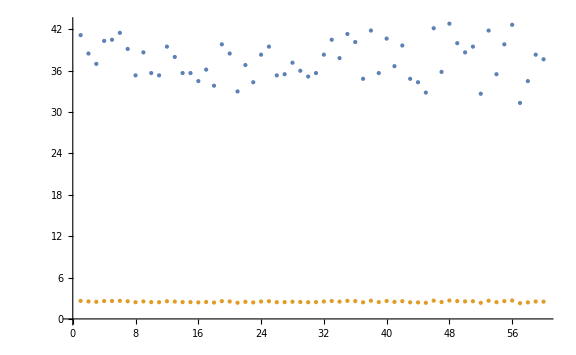

Pump Light: s+Pump, Energy: 27.49

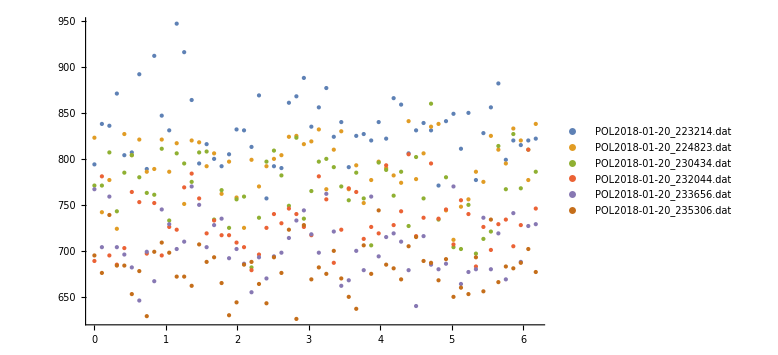

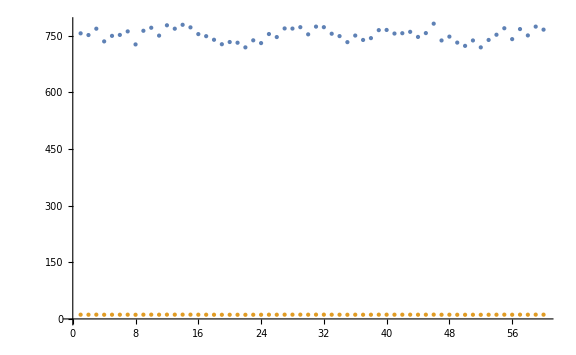

Pump Light: s+Pump, Energy: 36.55

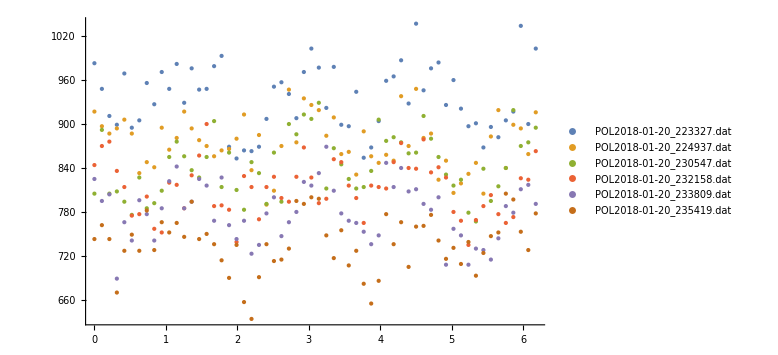

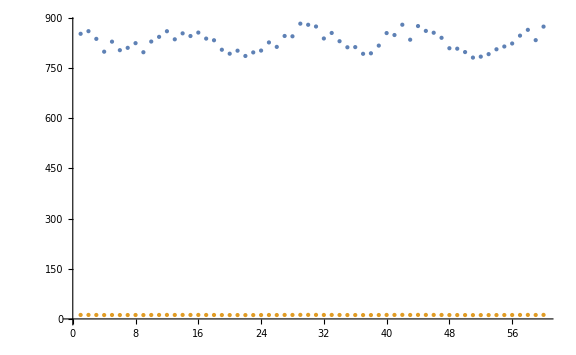

Pump Light: s-Pump, Energy: 22.63

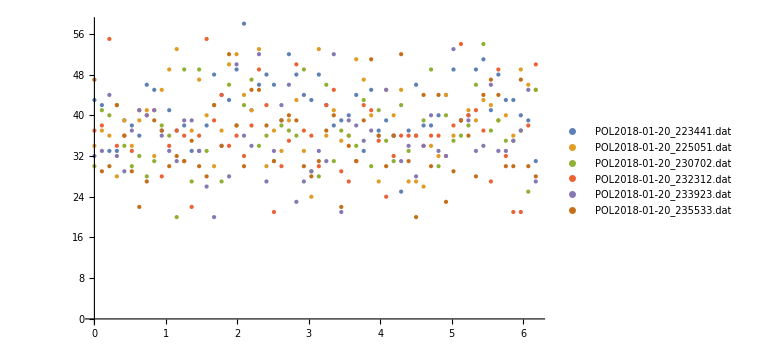

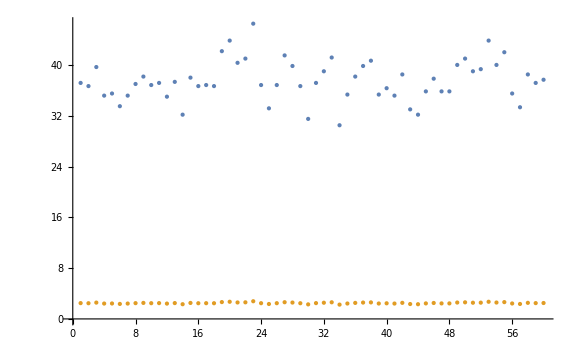

Pump Light: s-Pump, Energy: 27.49

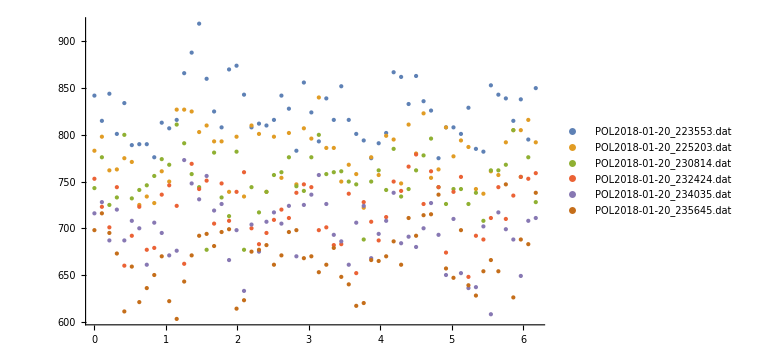

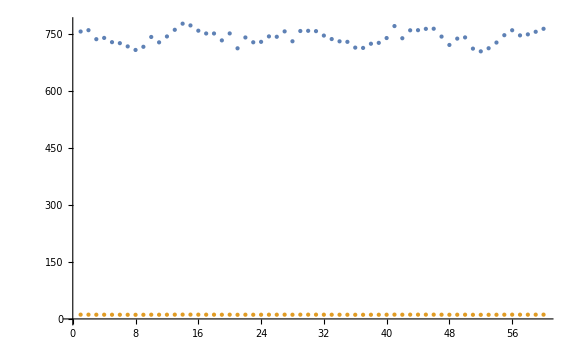

Pump Light: s-Pump, Energy: 36.55

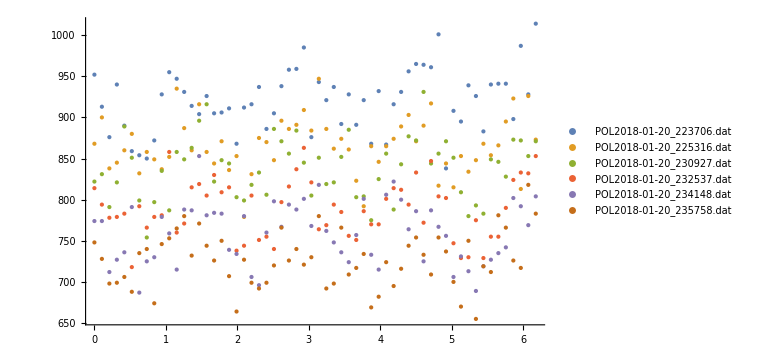

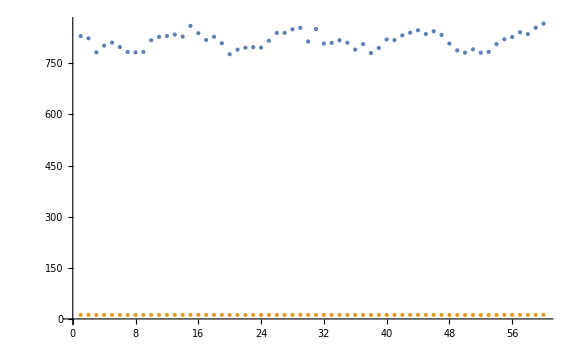

```mathematica
allStokes=<||>;
stokes=<||>;
For[j=1,j<=Length[allFiles],j++,
For[i=1,i<=Length[allFiles[[j]]],i++,
Print["Pump Light: "<>ToString[Keys[allFiles][[j]]]<>", Energy: "<>ToString[Keys[allFiles[[j]]][[i]]]]; 
Print[PlotListOfPolFileNames[allFiles[[j]][[i]]]];
Print[ListPlot[GetAverageCountRateFromFileNames[allFiles[[j]][[i]]]]];
AppendTo[stokes,Keys[allFiles[[j]]][[i]]->GetStokesFromFileNames[allFiles[[j]][[i]]]]
];
AppendTo[allStokes,Keys[allFiles][[j]]->stokes]
];
```

```mathematica
GetIndexOfFilenameFromTimestamp[polFileNames,"223327"]
```

10

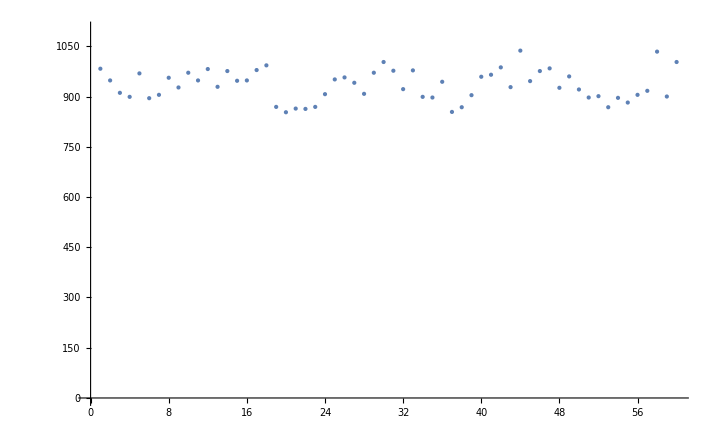

```mathematica
ListPlot[Normal[ImportFile[polFileNames[[10]]][[2]][All,"COUNT"]],PlotRange->{Automatic,{0,1100}}]
```

```mathematica
noPumpLowEng=allFiles["s-Pump"][[1]];
ImportFile[noPumpLowEng[[1]]]
stokes=GetStokesFromFileNames[noPumpLowEng];
ListPlot[Transpose[stokes],PlotLabel-> "Polarization Values Over Time",PlotRange->{-.1,.1},AxesLabel->{"Run Number","Percent Polarization"} ,PlotLegends->{"P_0","P_1","P_2","|P_3|","P_(3  C2)","P_(3  S2)"}];
PlotRawPolFromFileName[noPumpLowEng];
GetFourierCoefficientsFromFileNames[noPumpLowEng];
```

{<|#File→/home/pi/RbData/2018-01-20/POL2018-01-20_223441.dat,#Comments→Run,#IonGauge(Torr):→0.000176,#CVGauge(N2)(Torr):→1.05,#CVGauge(He)(Torr):→0.000984,#CURTEMP_R(degC):→140.,#SETTEMP_R(degC):→140.,#CURTEMP_T(degC):→199.9,#SETTEMP_T(degC):→200.,#AOUT:→516,#LEAKCURR:→0.0002,#AOUTCONV:→0.030938,#REV:→1,#DATAPPR:→60,#STPPERREV:→1200,#DATPTS:→60,#DWELL(s):→1|>,Dataset[<>]}

{<|#File→/home/pi/RbData/2018-01-20/POL2018-01-20_223706.dat,#Comments→Run,#IonGauge(Torr):→0.000176,#CVGauge(N2)(Torr):→1.05,#CVGauge(He)(Torr):→0.000995,#CURTEMP_R(degC):→140.,#SETTEMP_R(degC):→140.,#CURTEMP_T(degC):→199.9,#SETTEMP_T(degC):→199.9,#AOUT:→36,#LEAKCURR:→0.0002,#AOUTCONV:→0.030938,#REV:→1,#DATAPPR:→60,#STPPERREV:→1200,#DATPTS:→60,#DWELL(s):→1|>,Dataset[<>]}

74

145

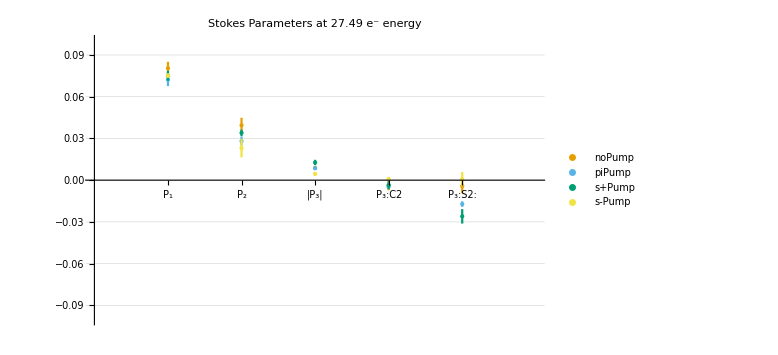
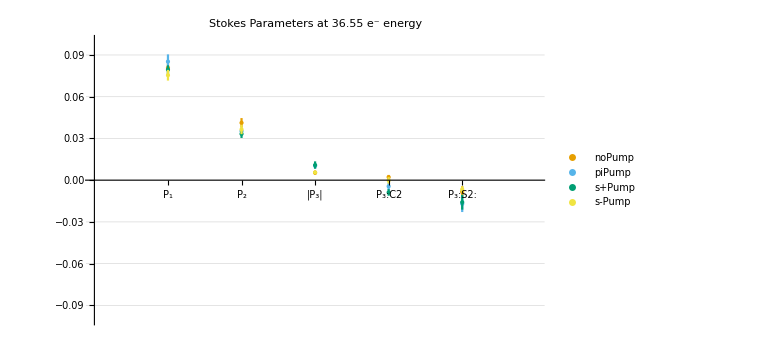
<|27.49→-Graphics-,36.55→-Graphics-|>

```mathematica
runs=6; (*The number of Electron Polarization Runs*)
energies={22.63,27.49,36.55}; (* A list of the AOUTs or energies at which we collected data*)
pumpLights={"noPump","piPump","s+Pump","s-Pump"};
excitationFile=GetIndexOfFilenameFromTimestamp[polFileNames,
startFile=GetIndexOfFilenameFromTimestamp[polFileNames,"013049"]
Length[polFileNames]
fileNames=<||>;
allFiles=<||>;

For[j=0,j<Length[pumpLights],j++,
For[i=startFile,i<Length[energies]+startFile,i++,
listONames=Take[polFileNames,{i+j*Length[energies],i+Length[energies]*runs*Length[pumpLights]-j-(i-startFile)-1,Length[energies]*Length[pumpLights]}];
AppendTo[fileNames,energies[[i-startFile+1]]->listONames];
];
AppendTo[allFiles,pumpLights[[j+1]]->fileNames];
];
allFiles;
energyPlots=<||>;

For[m=2,m≤Length[allFiles[[1]]],m++,
energyIndex=m;
darkCounts={ConstantArray[10,60],ConstantArray[3.3,60]};
stokes=<||>;
For[i=1,i≤Length[Keys[allFiles]],i++,
molyCounts=GetCurrentNormalizedAverageCountRateFromFileNames[allFiles[[i]][[1]]];
AppendTo[stokes,Keys[allFiles][[i]]->CalculateAverageStokesFromFilesAndCountRates[allFiles[[i]][[energyIndex]],molyCounts,darkCounts]];
];

plots={};

For[i=1,i≤Length[stokes],i++,
s=stokes[[i]];
plotData={};
For[k=2,k≤Length[s[[1]]],k++,
AppendTo[plotData,{{k-1,s[[1]][[k]]},ErrorBar[s[[2]][[k]]]}];
];
AppendTo[plots,ErrorListPlot[Legended[plotData,Keys[stokes][[i]]],GridLines->Automatic,ImageSize->{960,600},PlotRange->{{0,6},{-.1,.1}},PlotStyle->colorBlindPallete[[i]],Ticks->{{{1,"P_1"},{2,"P_2"},{3,"|P_3|"},{4,"P_3:C2"},{5,"P_3:S2:"}},Automatic}]];
];
AppendTo[energyPlots,Keys[allFiles[[1]]][[m]]->Show[plots,ImageSize->Large,PlotLabel->"Stokes Parameters at "<>ToString[Keys[allFiles[[1]]][[energyIndex]]]<>" e^- energy"]];
];
energyPlots
```

```mathematica
Rasterize[Show[energyPlots[[1]]],ImageResolution-> 200]
```

-Graphics-